# ComplexMapVisualization

Visualize the behavior of conformal mappings in the complex plane

## Definition

```mathematica
With[{
defaultImage=
Graphics[
Flatten[
{Thickness[0.01],
Green,
Table[InfiniteLine[{i,0},{0,1}],{i,0,1,.1}],
Red,
Table[InfiniteLine[{0,j},{1,0}],{j,0,1,.1}]}],
PlotRange->{{0,1},{0,1}}]},

Options[ComplexMapVisualization]={"Image"->defaultImage}

];
```

```mathematica
ComplexMapVisualization[func_,opts:OptionsPattern[{ComplexMapVisualization,ImageTransformation,Rasterize}]]:=
Block[
{
protectedComplexFunc,
complexMappingFunction,
image,
imageTransOps=FilterRules[{opts},Options[ImageTransformation]],
rasterOps=FilterRules[{opts},Options[Rasterize]]
},


protectedComplexFunc[z_?NumericQ]:=(func[z]);
complexMappingFunction=Function[coords,With[{val=protectedComplexFunc[N[coords.{1,I}]]},Mod[ReIm[val],1]]];

image=OptionValue["Image"];
If[!(Head[image]===Image&&ImageQ[image]),
image=Rasterize[image,"Image",rasterOps]];
ImageTransformation[image,complexMappingFunction,imageTransOps]
]
```

## Documentation

### Usage

ComplexMapVisualization[f]

returns the ImageTransformation of a given function f on the complex plane.

### Details & Options

f can be any function that accepts a complex number as input and returns a complex number as output.

ComplexMapVisualization inherits options from ImageTransformation and Rasterize, which are passed to those functions during evaluation.

ComplexMapVisualization also has an "Image" option, so that mappings can be visualized on different base images. The default image is a grid of red and green lines.

With default option settings, the image is mapped using a DataRange and PlotRange of {{0,1},{0,1}}.

## Examples

### Basic Examples

Visualize the sine function in the complex plane:

```mathematica
ComplexMapVisualization[Sin[2#]&]
```

-Graphics-

Mappings on different sections of the complex plane can be visualized by specifying a different DataRange or PlotRange:

```mathematica
ComplexMapVisualization[Sin,PlotRange->{{-Pi,Pi},{0,Pi}},RasterSize->200]
```

-Graphics-

Forward transformations can be created by using the inverse function:

```mathematica
ComplexMapVisualization[ArcSin,PlotRange->{{-Pi,Pi},{0,Pi}},RasterSize->200]
```

-Graphics-

### Scope

Standard special functions can be visualized:

```mathematica
ComplexMapVisualization[Gamma,PlotRange->{{-3,3},{-1,1}}]
```

-Graphics-

General functions that have complex values as their domain and range can be visualized:

```mathematica
ComplexMapVisualization[Function[z,(z-1)/(z^2+2)],PlotRange->{{-3,3},{-3,3}},RasterSize->150]
```

-Graphics-

Compiled functions can be visualized:

```mathematica
cf=Compile[{{x,_Complex}},Sin[x]+x^2-1/(1+x)]
```

CompiledFunction[…]

```mathematica
ComplexMapVisualization[cf,PlotRange->{{-1.5,1.5},{-1,1}}]
```

-Graphics-

### Options

The "Image" option can be set to visualize mappings on arbitrary images or graphics objects:

```mathematica
ComplexMapVisualization[Cosh,PlotRange->{{-2,2},{-2,2}},"Image"->ExampleData[{"TestImage","Mandrill"}],RasterSize->100]
```

-Graphics-

Use the "Image" option to see the transformation of a polar grid:

```mathematica
ComplexMapVisualization[ProductLog,PlotRange->{{-1,1},{-1,1}},"Image"->-Graphics-]
```

-Graphics-

Options available to Rasterize affect the quality of the resulting image:

```mathematica
ComplexMapVisualization[Cosh,PlotRange->{{-2,2},{-2,2}},"Image"->ExampleData[{"TestImage","Mandrill"}],RasterSize->20]
```

-Graphics-

### Properties and Relations

Using ParametricPlot on the inverse function gives a result similar to the one produced by ComplexMapVisualization:

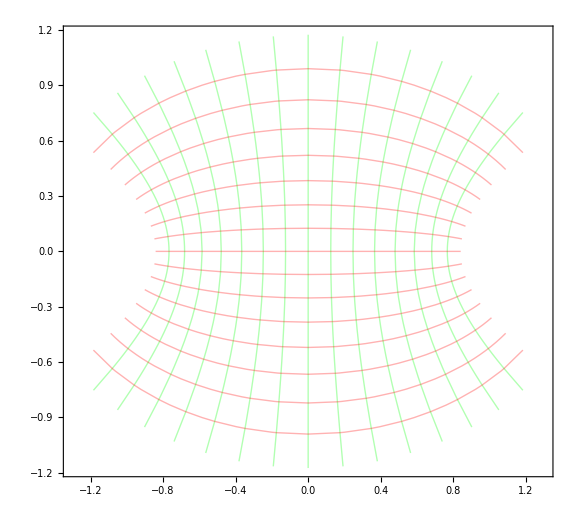

```mathematica
With[{f=ArcSin},{ComplexMapVisualization[f,PlotRange->{{-1,1},{-1,1}}],ParametricPlot[ReIm[InverseFunction[f][x+ⅈ y]],{x,-1,1},{y,-1,1},]}//GraphicsRow]
```

### Possible Issues

With a sufficiently large PlotRange, the computation may take a long time:

```mathematica
AbsoluteTiming[ComplexMapVisualization[Exp,PlotRange->{{-2,2},{-2,2}}]]
```

{27.7577,-Graphics-}

You can use the RasterSize option to reduce the quality of the input image and reduce the computation time:

```mathematica
AbsoluteTiming[ComplexMapVisualization[Exp,PlotRange->{{-2,2},{-2,2}},RasterSize->150]]
```

{3.40925,-Graphics-}

## Source & Additional Information

### Contributed By

Duncan Pettengill

### Keywords

Complex

Visualization

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

ComplexPlot

ImageForwardTransformation

ImageTransformation

ParametricPlot

### Related Resource Objects

ComplexBubblePlot

RiemannSphereComplexPlot

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

12.3+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

Credit to Oleg Marichev for highlighting the need for a good complex visualization function.

## Submission Notes

Additional information for the reviewer.